0.381098+0.273125 x

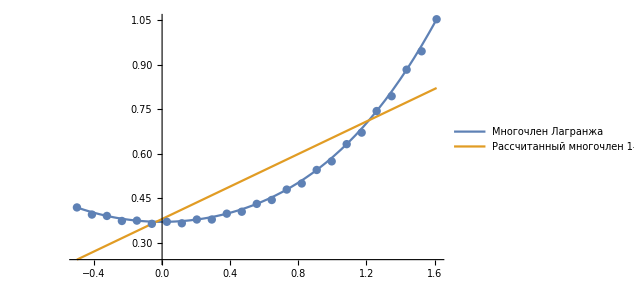

Сумма квадратов отклонений: 0.241996

0.355804-0.0275279 x+0.270371 x^2

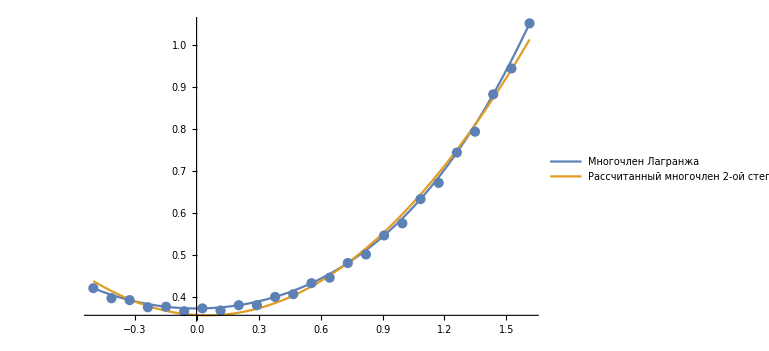

Сумма квадратов отклонений: 0.00479682

```mathematica
(*Вариант 4*)
(*Задание 3*)
data = {{-0.5,0.419945},{-0.412,0.395988},{-0.324,0.391402},{-0.236,0.374437},{-0.148,0.375642},{-0.06,0.364857},{0.028,0.371704},
{0.116,0.366656},{0.204,0.379343},{0.292,0.379343},{0.38,0.399032},{0.468,0.405545},{0.556,0.43196},{0.644,0.444969},{0.732,0.480039},
{0.82,0.500438},{0.908,0.545871},{0.996,0.574811},{1.084,0.632645},{1.172,0.67142},{1.26,0.743887},{1.348,0.793733},{1.436,0.882993},
{1.524,0.944755},{1.612,1.05247}};
n=Length[data]-1;
h=data[[2,1]]-data[[1,1]];
f[x_]:=0.371558-5.487052*^-6 x+0.185753 x^2+0.000312 x^3+0.030658 x^4-0.002526 x^5+0.007333 x^6-0.001714 x^7-0.016033 x^8+0.026884 x^9-0.020095 x^10+0.007345 x^11-0.001071 x^12;(*используем многочлен Лагранжа 12-й степени, подсчитанный ранее*)
Array[xdata,{n+1,0}]; Array[ydata,{n+1,0}];
For[i =0,i<=n,i++, xdata[i]=data[[i+1,1]];
ydata[i]=data[[i+1,1]];
];
(*найдём апроксмимрующий многочлен 1-го порядка*)
koefs=FindFit[data,a*x+b,{a,b},x];
y=a*x+b/.koefs
g[x_]:=0.381098+0.273125 x;
gr3:=Plot[{f[x],g[x]},{x,xdata[0],xdata[n]},
PlotLegends->{"Многочлен Лагранжа", "Рассчитанный многочлен 1-ой степени"}]
gr2:=ListPlot[data]
Show[{gr3,gr2}]
sumq = 0;
For[i=0,i<=n,i++,
sumq=sumq+Abs[g[xdata[i]]-f[xdata[i]]]^2;];
Print["Сумма квадратов отклонений: ",sumq];
(*Найдём апроксимирующий многочлен 2-го порядка*)
koefs=FindFit[data,p*x^2+q*x+c,{p,q,c},x];
y=p*x^2+q*x+c/.koefs
m[x_]:=0.355804-0.027528 x+0.270371 x^2;
gr3:=Plot[{f[x],m[x]},{x,xdata[0],xdata[n]},
PlotLegends->{"Многочлен Лагранжа", "Рассчитанный многочлен 2-ой степени"}]
gr2:=ListPlot[data]
Show[{gr3,gr2}]
sumq = 0;
For[i=0,i<=n,i++,
sumq=sumq+Abs[m[xdata[i]]-f[xdata[i]]]^2;];
Print["Сумма квадратов отклонений: ",sumq];
```